## Fixed M_Z'=10 TeV, Fixed Brane parameter = 0.4, Vary parameter C_ν_Ri^Z'

Γ (Z'→ν ν̄) =  (g_PQ^2 M_(Z '))/(12π) ((1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2+(1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2+2 m_ν^2/(M_(Z ')^2) (  (1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2-2 ( (1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2 )√(1-4 m_ν^2/M_Z'^2)

```mathematica
MassZprime10=10;
MassNu=0.1;
CvL04=-1/4(e^2/(sinsquared(1-sinsquared)))(0.001)+(0.4)
```

0.399871

```mathematica
Zprime10decayfixedmass04[CvR_]:=MassZprime10/(12π)(1/4(CvL04+CvR)^2+1/4(CvL04-CvR)^2+2(MassNu/MassZprime10)^2(1/4(CvL04+CvR)^2-1/2(CvL04+CvR)^2))√(1-4(MassNu/MassZprime10)^2)*10^3
Qmax=1.0;
Qmin=0.0;
Npt=10;
Q[i_]:=(Qmax-Qmin)/Npt*i+Qmin
```

```mathematica
Zprime10decayfixedmass04Table=Table[{Q[i],Zprime10decayfixedmass04[Q[i]]},{i,0,Npt}]
```

{{0.,21.2006},{0.1,22.5254},{0.2,26.5021},{0.3,33.1305},{0.4,42.4107},{0.5,54.3426},{0.6,68.9264},{0.7,86.162},{0.8,106.049},{0.9,128.588},{1.,153.779}}

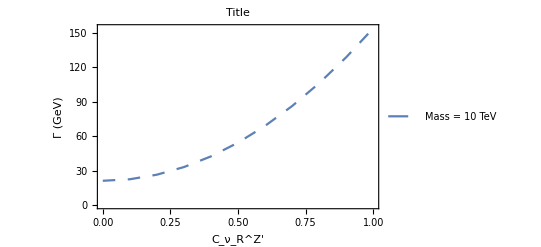

```mathematica
PlotZprimeDecayFixed1004=ListPlot[%, Joined-> True,PlotStyle->{Dashing[Medium]},PlotLegends->{"Mass = 10 TeV"},Frame->True,FrameLabel->{"C_ν_R^Z'","Γ (GeV)"},PlotLabel->HoldForm[Title],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

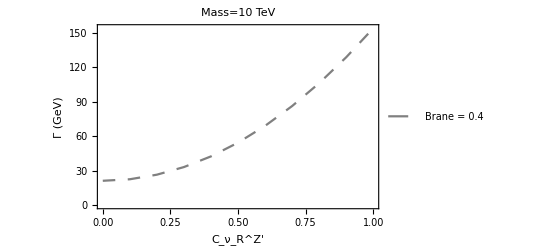

```mathematica
PlotZprimeDecayFixed1004B=ListPlot[%%, Joined-> True,PlotStyle->{Gray,Dashing[Medium]},PlotLegends->{"Brane = 0.4"},Frame->True,FrameLabel->{"C_ν_R^Z'","Γ (GeV)"},PlotLabel->HoldForm[Mass = 10 TeV],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

```mathematica
TableForm[Zprime10decayfixedmass04Table,TableHeadings-> {None,{"CvR","Decay Rate(GeV)"}}]
```

CvR | Decay Rate(GeV)
0. | 21.2006
0.1 | 22.5254
0.2 | 26.5021
0.3 | 33.1305
0.4 | 42.4107
0.5 | 54.3426
0.6 | 68.9264
0.7 | 86.162
0.8 | 106.049
0.9 | 128.588
1. | 153.779

## Fixed M_Z'=8 TeV, Fixed Brane parameter = 0.4, Vary parameter C_ν_Ri^Z'

Γ (Z'→ν ν̄) =  (g_PQ^2 M_(Z '))/(12π) ((1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2+(1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2+2 m_ν^2/(M_(Z ')^2) (  (1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2-2 (1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2 )√(1-4 m_ν^2/M_Z'^2)

```mathematica
MassZprime8=8;
MassNu=0.1;
CvL04=-1/4(e^2/(sinsquared(1-sinsquared)))(0.001)+(0.4)
```

0.399871

```mathematica
Zprime8decayfixedmass04[CvR_]:=MassZprime8/(12π)(1/4(CvL04+CvR)^2+1/4(CvL04-CvR)^2+2(MassNu/MassZprime8)^2(1/4(CvL04+CvR)^2-1/2(CvL04+CvR)^2))√(1-4(MassNu/MassZprime8)^2)*10^3
Qmax=1.0;
Qmin=0.0;
Npt=10;
Q[i_]:=(Qmax-Qmin)/Npt*i+Qmin
```

```mathematica
Zprime8decayfixedmass04Table=Table[{Q[i],Zprime8decayfixedmass04[Q[i]]},{i,0,Npt}]
```

{{0.,16.9576},{0.1,18.0168},{0.2,21.1971},{0.3,26.4985},{0.4,33.9209},{0.5,43.4644},{0.6,55.129},{0.7,68.9146},{0.8,84.8213},{0.9,102.849},{1.,122.998}}

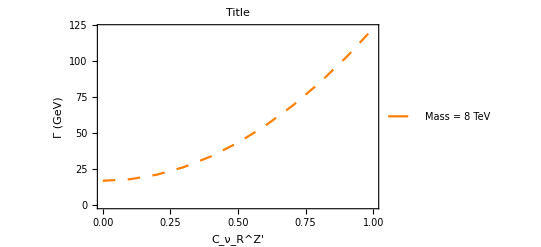

```mathematica
PlotZprimeDecayFixed804=ListPlot[%, Joined-> True,PlotStyle->{Orange, Dashing[Medium]},PlotLegends->{"Mass = 8 TeV"},Frame->True,FrameLabel->{"C_ν_R^Z'","Γ (GeV)"},PlotLabel->HoldForm[Title],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

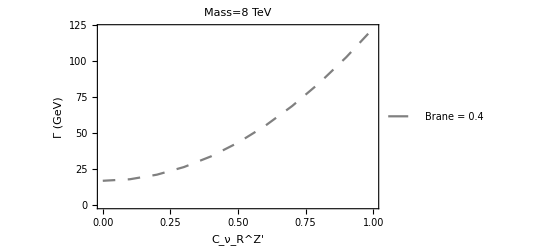

```mathematica
PlotZprimeDecayFixed804B=ListPlot[%%, Joined-> True,PlotStyle->{Gray,Dashing[Medium]},PlotLegends->{"Brane = 0.4"},Frame->True,FrameLabel->{"C_ν_R^Z'","Γ (GeV)"},PlotLabel->HoldForm[Mass = 8 TeV],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

```mathematica
TableForm[Zprime8decayfixedmass04Table,TableHeadings-> {None,{"CvR","Decay Rate(GeV)"}}]
```

CvR | Decay Rate(GeV)
0. | 16.9576
0.1 | 18.0168
0.2 | 21.1971
0.3 | 26.4985
0.4 | 33.9209
0.5 | 43.4644
0.6 | 55.129
0.7 | 68.9146
0.8 | 84.8213
0.9 | 102.849
1. | 122.998

## Fixed M_Z'=5 TeV, Fixed Brane parameter = 0.4, Vary parameter C_ν_Ri^Z'

Γ (Z'→ν ν̄) =  (g_PQ^2 M_(Z '))/(12π) ((1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2+(1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2+2 m_ν^2/(M_(Z ')^2) (  (1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2-2 (1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2 )√(1-4 m_ν^2/M_Z'^2)

```mathematica
MassZprime5=5;
MassNu=0.1;
CvL04=-1/4(e^2/(sinsquared(1-sinsquared)))(0.001)+(0.4)
```

0.399871

```mathematica
Zprime5decayfixedmass04[CvR_]:=MassZprime5/(12π)(1/4(CvL04+CvR)^2+1/4(CvL04-CvR)^2+2(MassNu/MassZprime5)^2(1/4(CvL04+CvR)^2-1/2(CvL04+CvR)^2))√(1-4(MassNu/MassZprime5)^2)*10^3
Qmax=1.0;
Qmin=0.0;
Npt=10;
Q[i_]:=(Qmax-Qmin)/Npt*i+Qmin
```

```mathematica
Zprime5decayfixedmass04Table=Table[{Q[i],Zprime5decayfixedmass04[Q[i]]},{i,0,Npt}]
```

{{0.,10.5908},{0.1,11.251},{0.2,13.2359},{0.3,16.5456},{0.4,21.1799},{0.5,27.1389},{0.6,34.4226},{0.7,43.0311},{0.8,52.9642},{0.9,64.222},{1.,76.8046}}

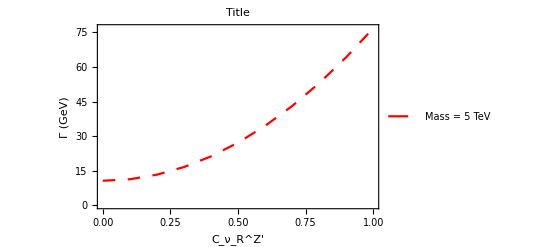

```mathematica
PlotZprimeDecayFixed504=ListPlot[%, Joined-> True,PlotStyle->{Red, Dashing[Medium]},PlotLegends->{"Mass = 5 TeV"},Frame->True,FrameLabel->{"C_ν_R^Z'","Γ (GeV)"},PlotLabel->HoldForm[Title],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

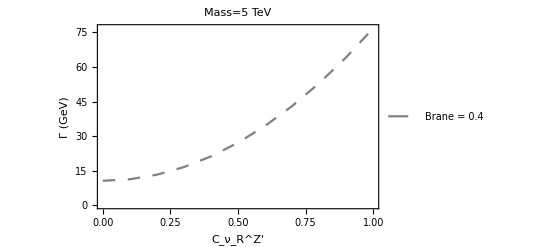

```mathematica
PlotZprimeDecayFixed504B=ListPlot[%%, Joined-> True,PlotStyle->{Gray,Dashing[Medium]},PlotLegends->{"Brane = 0.4"},Frame->True,FrameLabel->{"C_ν_R^Z'","Γ (GeV)"},PlotLabel->HoldForm[Mass = 5 TeV],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

```mathematica
TableForm[Zprime5decayfixedmass04Table,TableHeadings-> {None,{"CvR","Decay Rate(GeV)"}}]
```

CvR | Decay Rate(GeV)
0. | 10.5908
0.1 | 11.251
0.2 | 13.2359
0.3 | 16.5456
0.4 | 21.1799
0.5 | 27.1389
0.6 | 34.4226
0.7 | 43.0311
0.8 | 52.9642
0.9 | 64.222
1. | 76.8046

## OverLay

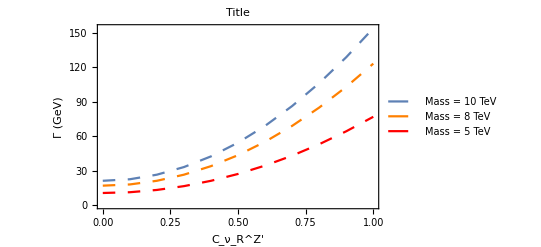

```mathematica
Show[PlotZprimeDecayFixed1004,PlotZprimeDecayFixed804,PlotZprimeDecayFixed504]
```

## OverLay 2

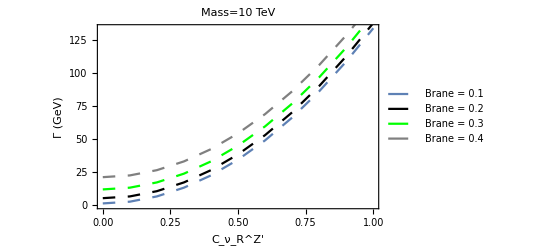

```mathematica
Show[PlotZprimeDecayFixed1001B,PlotZprimeDecayFixed1002B,PlotZprimeDecayFixed1003B,PlotZprimeDecayFixed1004B]
```

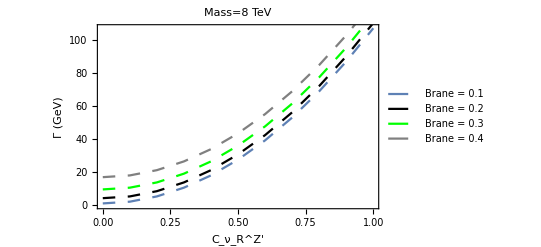

```mathematica
Show[PlotZprimeDecayFixed801B,PlotZprimeDecayFixed802B,PlotZprimeDecayFixed803B,PlotZprimeDecayFixed804B]
```

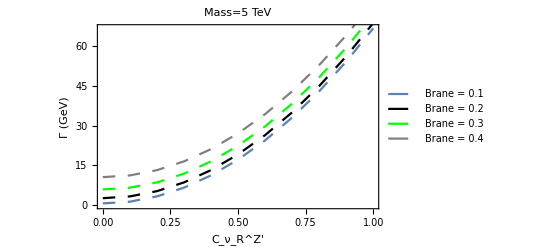

```mathematica
Show[PlotZprimeDecayFixed501B,PlotZprimeDecayFixed502B,PlotZprimeDecayFixed503B,PlotZprimeDecayFixed504B]
```